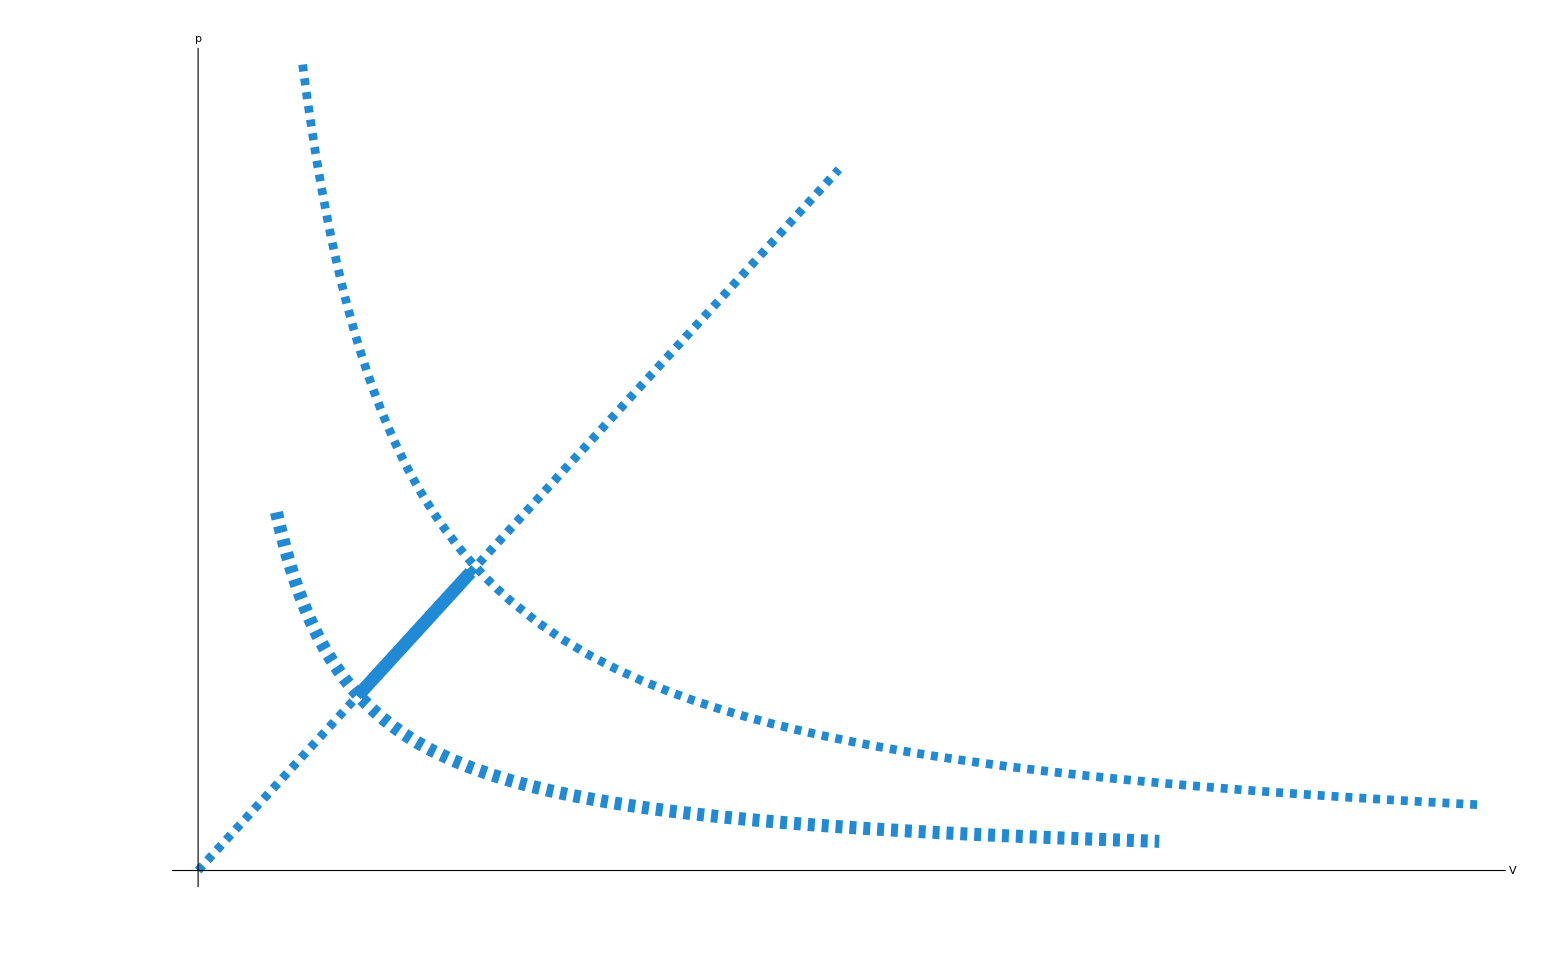

```mathematica
f[x_]:=2x
g[x_]:=2x
h[x_]:=0.5/x
i[x_]:=1.5/x
Show[{Plot[f[x],{x,0.5,0.85},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}],Plot[g[x],{x,0,2},PlotStyle->{Thickness[0.004],RGBColor["#218ad4"],Dashed}],Plot[h[x],{x,0,3},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"],Dashed}],Plot[i[x],{x,0,4},PlotStyle->{Thickness[0.004],RGBColor["#218ad4"],Dashed}]},PlotRange->All,AxesOrigin->{0,0},LabelStyle->Directive[Black,50], AxesLabel->{V,p},AxesStyle-> Thick,Ticks->{{{300,3},{450,50}}, {{8,8},{12,12}}},ImageSize->2000]
```

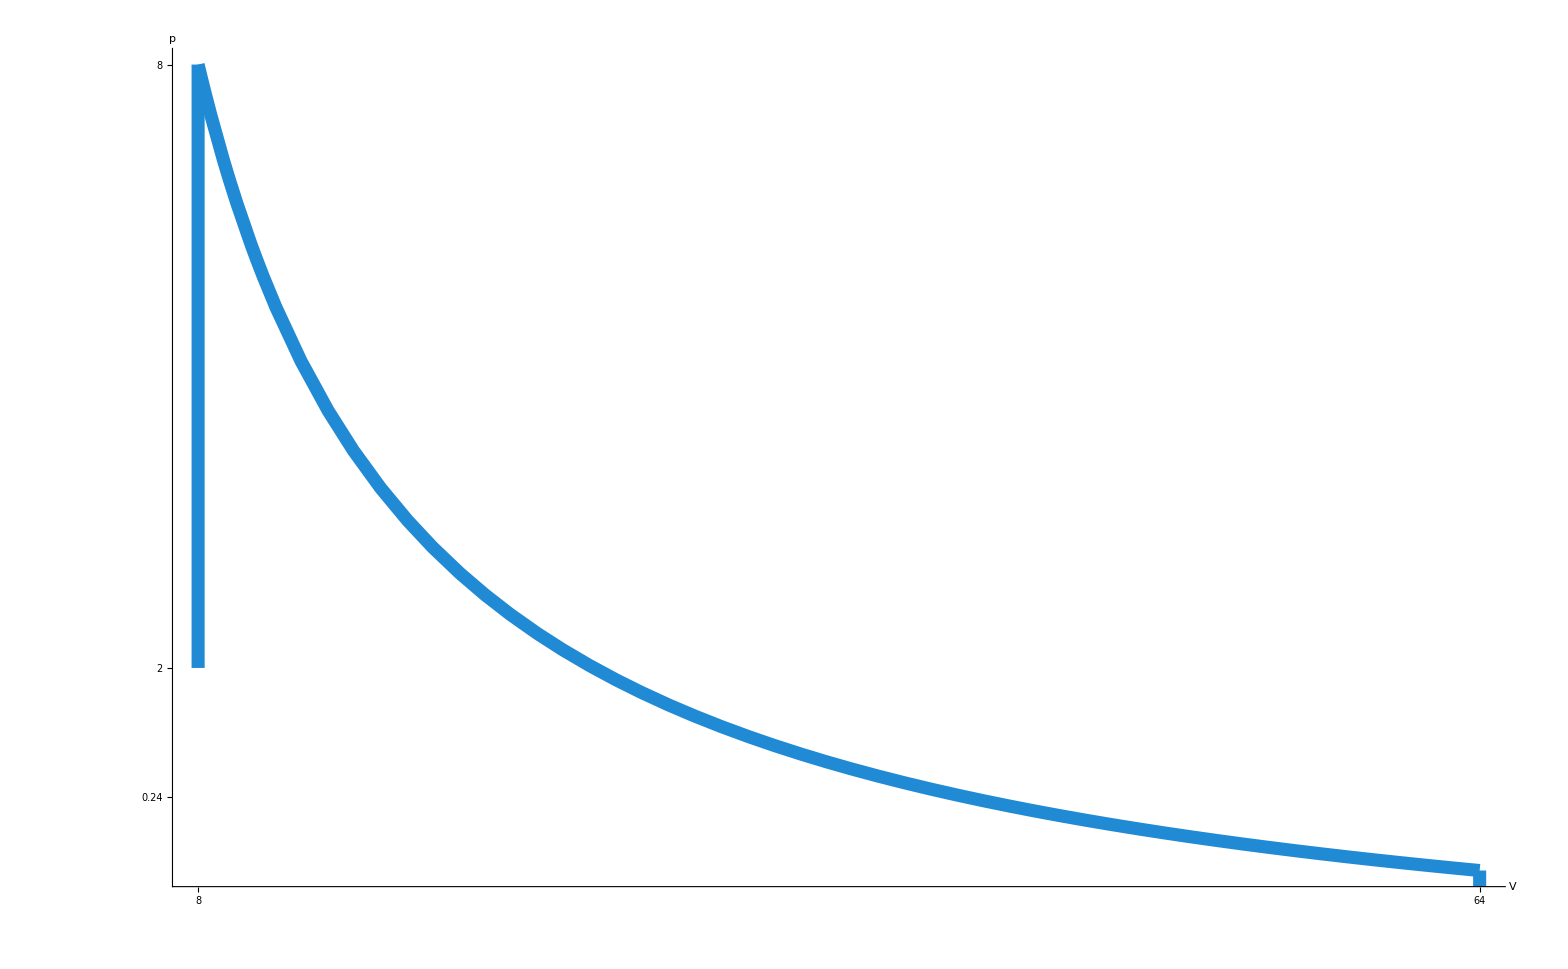

```mathematica
f[x_]:=1/x
g[x_]:=1/x
h[x_]:=3.3
i[x_]:=3.3/x
Show[{Plot[i[x],{x,0.15,1},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}]},PlotRange->All,AxesOrigin->{0,0},LabelStyle->Directive[Black,50], AxesLabel->{V,p},AxesStyle-> Thick, Epilog->{Thickness[0.006],RGBColor["#218ad4"],Line[{{1,1},{1,3.3}}],Line[{{0.15,8},{0.15,22}}]},Ticks->{{{0.15,8},{1,64}}, {{22,8},{5,0.24},{8,2},{1,0.15}}},ImageSize->2000]
```

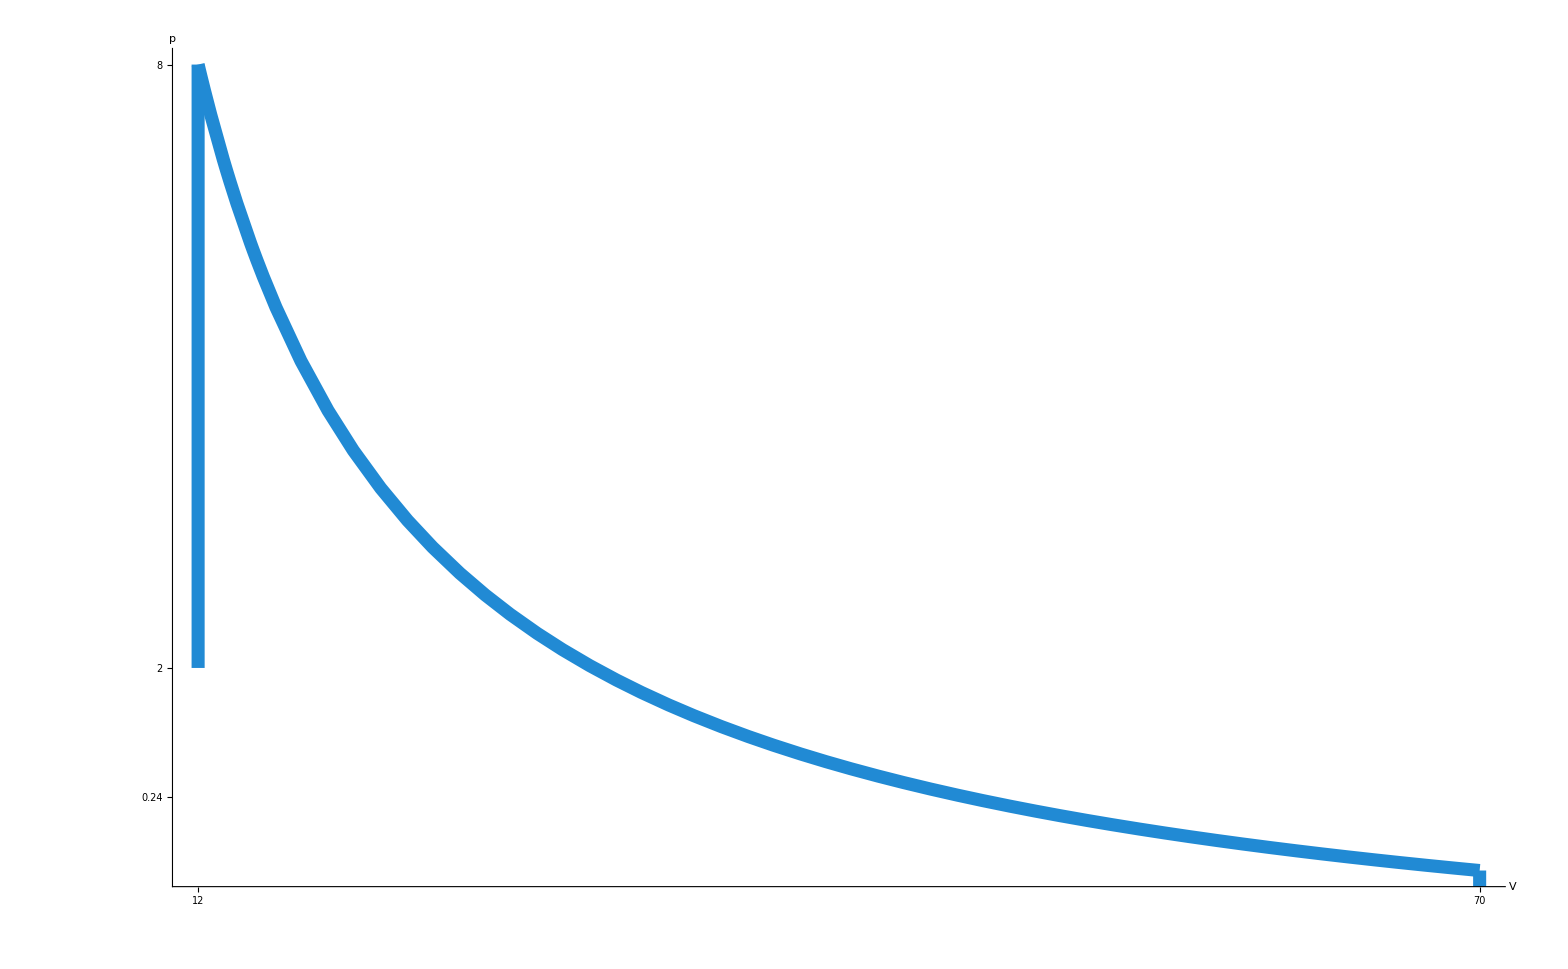

```mathematica
f[x_]:=1/x
g[x_]:=1/x
h[x_]:=3.3
i[x_]:=3.3/x
Show[{Plot[i[x],{x,0.15,1},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}]},PlotRange->All,AxesOrigin->{0,0},LabelStyle->Directive[Black,50], AxesLabel->{V,p},AxesStyle-> Thick, Epilog->{Thickness[0.006],RGBColor["#218ad4"],Line[{{1,1},{1,3.3}}],Line[{{0.15,8},{0.15,22}}]},Ticks->{{{0.15,12},{1,70}}, {{22,8},{5,0.24},{8,2},{1,0.15}}},ImageSize->2000]
```